### First Experiments

Is it possible that Central Binomial limits have some group structure? These seem to suggest the possibility. (with the operation of composing with the catalan (or other asymptotically equivalent sequences) and then taking a p-adic limit being the homomorphism from the group of integer sequences) If so it cannot be an isomorphism.
Update: THIS BREAKS FOR SO MANY REASONS:
Perhaps we should just consider integer sequences which converge p-adically to zero? What then?

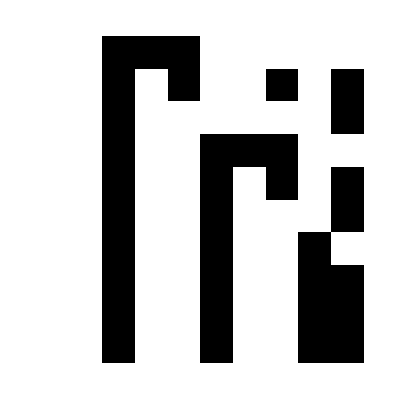

```mathematica
Module[{p=2,digits=10,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[p^(2n)]*CatalanNumber[p^(n)],p^digits],p,digits]],{n,1,rows}]]]
```

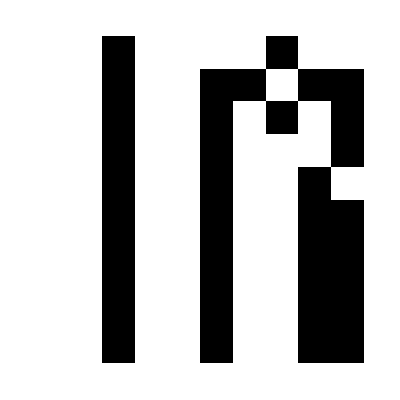

```mathematica
Module[{p=2,digits=10,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[p^(2n)+p^n],p^digits],p,digits]],{n,1,rows}]]]
```

```mathematica
Module[{p=2,digits=10,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[p^(2n)+p^n],p^digits],p,digits]],{n,1,rows}]]]
```

Let’s see if it works for constant multiple sequences as well.

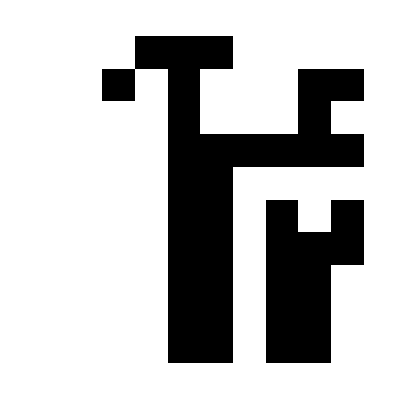

```mathematica
Module[{p=2,digits=10,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[3p^(2n)+5p^n],p^digits],p,digits]],{n,1,rows}]]]
```

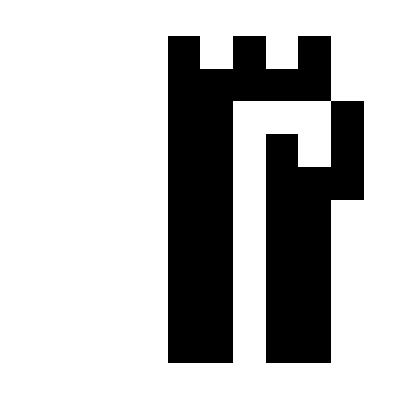

```mathematica
Module[{p=2,digits=10,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[3p^(2n)]*CatalanNumber[5p^n],p^digits],p,digits]],{n,1,rows}]]]
```

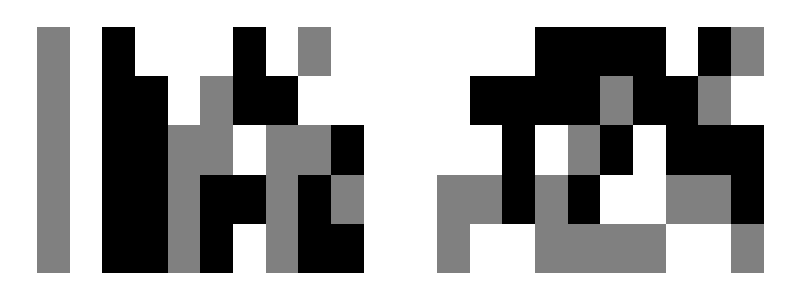

```mathematica
L1=Module[{p=3,digits=10,rows=5,a=90,c=12,b=1,d=2},Grid[{{ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[a*p^(b*n)]*CatalanNumber[c*p^(d*n)],p^digits],p,digits]],{n,1,rows}]],ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[a*p^(b*n)+c*p^(d*n)],p^digits],p,digits]],{n,1,rows}]]}}]]
```

### Experimenting with varying multiplication factors

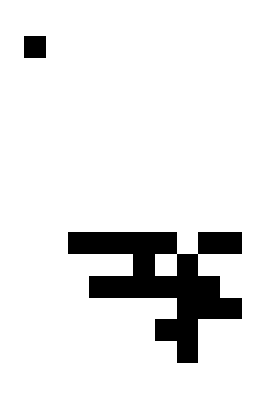

```mathematica
L2=Module[{p=2,digits=10,rows=15},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[p^(n)],p^digits],p,digits]],{n,1,rows}]]]
```

### Mixing Primes

Conjecture: mixing primes gives a limit of zero

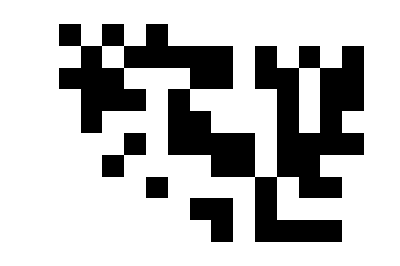

```mathematica
L3=Module[{p=2,digits=15,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[p^n+3^n],p^digits],p,digits]],{n,1,rows}]]]
```

### higher order limits

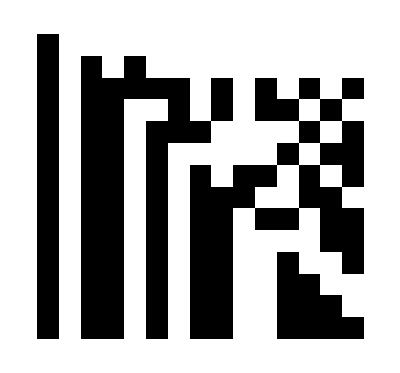

```mathematica
L4=Module[{p=2,digits=15,rows=15,r=3},Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[p^n-r]/p^(n-Ceiling[Log[p,r]]),p^digits],p,digits]],{n,Ceiling[Log[p,r]],rows}]];
ArrayPlot[L4]
```

```mathematica
FromDigits[Last[L4],2]
```

23247